```mathematica
(*Define the normalized Fourier transforms of the Chebyshev polynomials*)
Y[n_,y_]:=Module[{f},f=Sqrt[(-1)^n] ChebyshevT[n,x] Exp[-I x y];
Integrate[f,{x,-1,1}]/Sqrt[(4 Pi (2 n^2-1))/(4 n^2-1)]]

(*Define the inner product*)
InnerProd[n_,m_]:=Integrate[Y[n,y] Conjugate[Y[m,y]],{y,-Infinity,Infinity}]

(*Define Gram-Schmidt process*)
GramSchmidt[vecList_]:=Module[{n,m,inner,projection,u,v,orthoList={}},For[n=1,n≤Length[vecList],n++,v=vecList[[n]];
projection=0;
For[m=1,m<n,m++,u=orthoList[[m]];
inner=Integrate[u v,{y,-Infinity,Infinity}];
projection=projection+inner u;];
u=Simplify[v-projection];
u=Simplify[u/Sqrt[Integrate[u Conjugate[u],{y,-Infinity,Infinity}]]];
AppendTo[orthoList,u];];
orthoList]

(*Generate the function list*)
funcList=Table[Y[n,y],{n,0,20}];

(*Apply Gram-Schmidt process*)
orthoFuncs=GramSchmidt[funcList];

(*Output the orthogonalized functions*)
orthoFuncs
```

{Sin[y]/(√π y),(√(3/π) (-y Cos[y]+Sin[y]))/y^2,(√(5/π) (3 y Cos[y]+(-3+y^2) Sin[y]))/y^3,-(√(7/π) (y (-15+y^2) Cos[y]+3 (5-2 y^2) Sin[y]))/y^4,(3 (5 y (-21+2 y^2) Cos[y]+(105-45 y^2+y^4) Sin[y]))/(√π y^5),(√(11/π) (-y (945-105 y^2+y^4) Cos[y]+15 (63-28 y^2+y^4) Sin[y]))/y^6,(√(13/π) (21 y (495-60 y^2+y^4) Cos[y]+(-10395+4725 y^2-210 y^4+y^6) Sin[y]))/y^7,(√(15/π) (-y (-135135+17325 y^2-378 y^4+y^6) Cos[y]+7 (-19305+8910 y^2-450 y^4+4 y^6) Sin[y]))/y^8,(√(17/π) (9 y (-225225+30030 y^2-770 y^4+4 y^6) Cos[y]+(2027025-945945 y^2+51975 y^4-630 y^6+y^8) Sin[y]))/y^9,(√(19/π) (-y (34459425-4729725 y^2+135135 y^4-990 y^6+y^8) Cos[y]+45 (765765-360360 y^2+21021 y^4-308 y^6+y^8) Sin[y]))/y^10,(√(21/π) (55 y (11904165-1670760 y^2+51597 y^4-468 y^6+y^8) Cos[y]+(-654729075+310134825 y^2-18918900 y^4+315315 y^6-1485 y^8+y^10) Sin[y]))/y^11,1/y^12 √(23/π) (-y (-13749310575+1964187225 y^2-64324260 y^4+675675 y^6-2145 y^8+y^10) Cos[y]+33 (-416645775+198402750 y^2-12530700 y^4+229320 y^6-1365 y^8+2 y^10) Sin[y]),1/(√π y^13)5 (39 y (-8108567775+1175154750 y^2-40291020 y^4+471240 y^6-1925 y^8+2 y^10) Cos[y]+(316234143225-151242416325 y^2+9820936125 y^4-192972780 y^6+1351350 y^8-3003 y^10+y^12) Sin[y]),-1/y^14 3 √(3/π) (y (7905853580625-1159525191825 y^2+41247931725 y^4-523783260 y^6+2552550 y^8-4095 y^10+y^12) Cos[y]-91 (86877511875-41701205700 y^2+2770007625 y^4-57558600 y^6+454410 y^8-1320 y^10+y^12) Sin[y]),1/y^15 √(29/π) (105 y (2032933777875-301175374500 y^2+11043097065 y^4-149652360 y^6+831402 y^8-1768 y^10+y^12) Cos[y]+(-213458046676875+102776096548125 y^2-6957151150950 y^4+151242416325 y^6-1309458150 y^8+4594590 y^10-5460 y^12+y^14) Sin[y]),1/y^16 √(31/π) (-y (-6190283353629375+924984868933125 y^2-34785755754750 y^4+496939367925 y^6-3055402350 y^8+7936110 y^10-7140 y^12+y^14) Cos[y]+15 (-412685556908625+199227510231750 y^2-13703479539750 y^4+309206717820 y^6-2880807930 y^8+11639628 y^10-18564 y^12+8 y^14) Sin[y]),1/y^17 √(33/π) (17 y (-11288163762500625+1699293469623750 y^2-65293049571750 y^4+974390917500 y^6-6495939450 y^8+19606860 y^10-23940 y^12+8 y^14) Cos[y]+(191898783962510625-92854250304440625 y^2+6474894082531875 y^4-150738274937250 y^6+1490818103775 y^8-6721885170 y^10+13226850 y^12-9180 y^14+y^16) Sin[y]),1/y^18 √(35/π) (-y (6332659870762850625-959493919812553125 y^2+37554385678684875 y^4-581419060472250 y^6+4141161399375 y^8-14054850810 y^10+21366450 y^12-11628 y^14+y^16) Cos[y]+153 (41389933795835625-20067846688890000 y^2+1416077891353125 y^4-33855655333500 y^6+351863386875 y^8-1732250520 y^10+3993990 y^12-3800 y^14+y^16) Sin[y]),1/y^19 √(37/π) (171 y (1296158453080115625-197509859516970000 y^2+7855505776243125 y^4-125495023153500 y^6+944475406875 y^8-3522519000 y^10+6322470 y^12-4760 y^14+y^16) Cos[y]+(-221643095476699771875+107655217802968460625 y^2-7675951358500425000 y^4+187771928393424375 y^6-2034966711652875 y^8+10767019638375 y^10-28109701620 y^12+33575850 y^14-14535 y^16+y^18) Sin[y]),1/y^20 √(39/π) (-y (-8200794532637891559375+1255977541034632040625 y^2-50661278966102805000 y^4+831561397170879375 y^6-6557114959770375 y^8+26428139112375 y^10-54057118500 y^12+51482970 y^14-17955 y^16+y^18) Cos[y]+95 (-86324152975135700625+41995533879795746250 y^2-3021900850609641000 y^4+75412855451934000 y^6-847091406286125 y^8+4760156050650 y^10-13737824100 y^12+19509336 y^14-11781 y^16+2 y^18) Sin[y]),1/y^21 √(41/π) (105 y (-3046009397836931150625+468616830436450946250 y^2-19138705387194393000 y^4+321658914070494000 y^6-2639877451336125 y^8+11354311618650 y^10-25815032100 y^12+29418840 y^14-14421 y^16+2 y^18) Cos[y]+(319830986772877770815625-155815096120119939628125 y^2+11303797869311688365625 y^4-287080580807915895000 y^6+3326245588683517500 y^8-19671344879311125 y^10+61665657928875 y^12-100391791500 y^14+77224455 y^16-21945 y^18+y^20) Sin[y])}

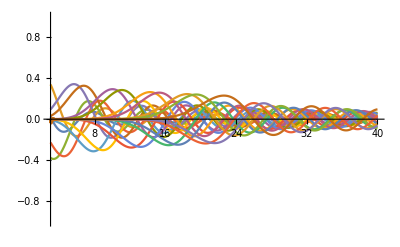

```mathematica
Plot[orthoFuncs,{y,3,40},PlotRange->{{3,40},{-1,1}}]
```

```mathematica
Integrate[orthoFuncs[[3]]^2,{y,-Infinity,Infinity}]
```

1

```mathematica
Integrate[orthoFuncs[[3]]*orthoFuncs[[4]],{y,-Infinity,Infinity}]
```

0

```mathematica
Limit[orthoFuncs[[5]],y->0]
```

```mathematica
Table[Integrate[orthoFuncs[[2n-1]]*BesselJ[0,y],{y,-Infinity,Infinity}],{n,1,9}]
```

{√π,(√(5 π))/4,(27 √π)/64,(25 √(13 π))/256,(1225 √(17 π))/16384,(3969 √(21 π))/65536,(266805 √π)/1048576,(184041 √(29 π))/4194304,(41409225 √(33 π))/1073741824}

```mathematica
N[Out[43]]
```

{1.77245,0.990832,0.747754,0.624089,0.546406,0.49191,0.450992,0.418821,0.392671}

```mathematica
FindGeneratingFunction[Out[43],n]
```

FindGeneratingFunction[{√π,(√(5 π))/4,(27 √π)/64,(25 √(13 π))/256,(1225 √(17 π))/16384,(3969 √(21 π))/65536,(266805 √π)/1048576,(184041 √(29 π))/4194304,(41409225 √(33 π))/1073741824},n]

```mathematica
alpha[m_,n_]:=Piecewise[{{(-1)^m,n==1},{(-1)^(m+1)*m^2,n==2}},(-1)^(m+n-1)*2^(n-2)*m*(2^(3-2n)*(m+n-2)!)/(FactorialPower[1/2,n-1]*(m-n+1)!)]
```

```mathematica
Tm[m_,y_]:=Sqrt[(-1)^m]*Sum[alpha[m,n]*(Exp[I*y]/(I*y)^n+(-1)^(m+n)*Exp[-I*y]/(I*y)^n),{n,1,m+1}]/Sqrt[(4 Pi (2 m^2-1))/(4 m^2-1)]
```

```mathematica
FullSimplify[Tm[1,y]]
```

(√(3/π) (-y Cos[y]+Sin[y]))/y^2

```mathematica
Y[1,y]
```

(√(3/π) (-y Cos[y]+Sin[y]))/y^2